## 5 - Introduction to Explanatory Data Visualisation: The Who, the What, and the How

Explanatory data visualisation is the art and science of communicating data effectively with images. Like every form of communication, it aims at influencing people in some way. Effective communication involves a lot more than just “presenting data”. You always want something from your audience. Maybe you want to convince them that global warming is real and that we have to do something about it; maybe you want to convince a panel that they should fund your research, or your non-profit. Whatever the case, you always have some goal you want to achieve when you create a chart, or a whole presentation. Making those goals clear will focus your work and result in better visualisations.

Before you even start creating a plot meant to be presented to other people, you should ask yourself three questions:

Who is your audience? What do they care about, and what do they know?

What data are you going to show them, and what do you want to achieve?

How are you going to show your data? What is the most effective way to present the data for that audience in order to achieve your goal?

Let us illustrate these questions with two examples that we have seen before.

### Tickets processing

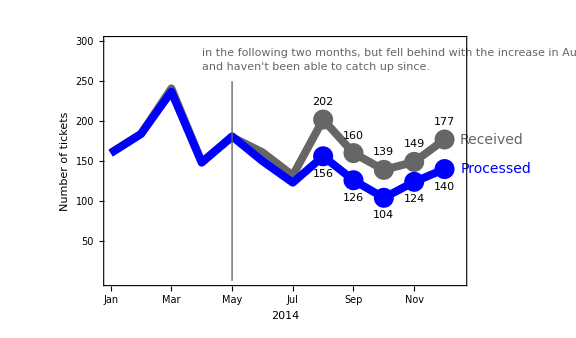

Who: decision-makers in a company, who are familiar with the company’s work, and have the power to hire new employees.

What: We want to demonstrate that after losing two people in May, our team has not been able to keep up with the work of processing tickets. Our goal is to convince them to hire people to replace those we have lost.

How: We will show them a plot comparing the number of tickets received versus the number of tickets processed, which will make it clear that after May we lost the capacity to process all tickets we receive.

### Summer school program

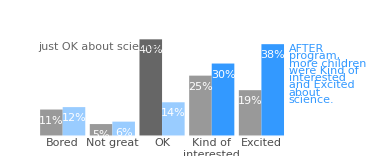

Who: decision-makers in a school, who can fund summer programmes.

What: We want to demonstrate that the program has been successful in raising the interest of children in science. Our goal is to convince them to fund the continuation and expansion of the programme.

How: We will show them a plot comparing the interest of children in science before and after they went through the programme, highlighting their resulting increase in interest for science.

### The 3-minute pitch and the one-sentence pitch

The 3-minute pitch is a technique that we can use to narrow down what we want to achieve with our presentation. The idea is to summarize the story we want to tell with our graph, and what we want from it, in a paragraph or so or text. For example, the 3-minute pitch for the first example above could be this:

Two people in our team left in May. For the next couple of months, we were able to still process the tickets, but then the volume increased, and we have not been able to keep up with the volume since. This has persisted for the past few months, and shows no sign of improving. It is clear that we need to hire two people to replace those we have lost if we want to go back to normal operations.

An extreme version of this is the one-sentence pitch. As the name implies, it consists of boiling down what we want to show and what we want to happen in a sentence (or two):

We haven’t been able to keep up with the tickets since we lost two people in May; we need to hire people to replace those we have lost.

A good one-sentence pitch can often be used inside a graph to help push your message. 

When you can’t write a good 3-minute pitch and one-sentence pitch, that is a sure sign that you don’t have a clear idea of what you want to show or achieve with a graph. Along with the three questions (who, what, and how), these should be your first steps in planning a visual.

## How? Choosing the right visual

The question how is what we will be spending most of our time addressing in this course. We will cover many factors involved in creating a compelling visual, including how to emphasize and de-emphasize parts of a graph, identifying and getting rid of visual distractions and clutter in graphs, aesthetics, how to make our graph tell a story visually, and others. The first decision in deciding how to present a graph, however, is one of the most important: what kind of graph you will use. Is is a bar chart? a line plot? Or something else?

We have already been introduced to some of the most useful kinds of graphs, and we have learned what they are good at. For example, if the data you will show is a time series, a line plot is probably the choice; if you are comparing quantities of a few elements of a category, bar charts are usually the best choice.

To illustrate the results you can get when you do not choose the right graph to display your data, we will go back to the two examples we have been using, and show the plots people involved in those projects initially made:

### Tickets processing project

#### Before:

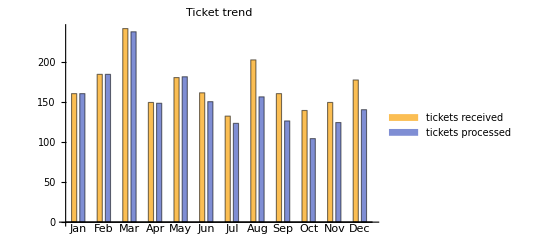

#### After:

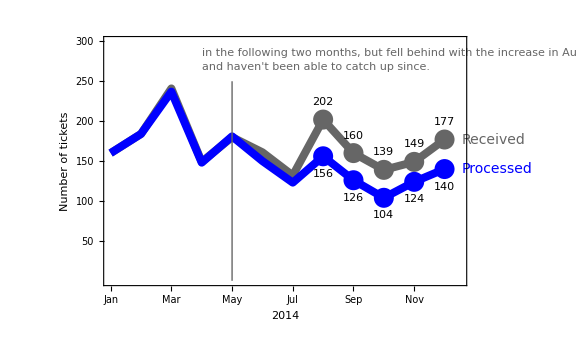

### Summer school project

#### Before:

```mathematica
-Graphics--Graphics-"Survey results"
```

#### After:

Choosing the right graph to display your data is the first step in creating a compelling visual. There is one situation, however, when you probably don’t need a graph at all...

### Only one or two numbers? Just show them!

If you only have one or two numbers, a graph is probably unnecessary, and in fact may be distracting. Compare these two visuals:

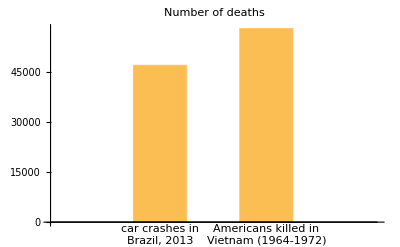

```mathematica
data = {47000, 58000};
labels = {"car crashes in\nBrazil, 2013", "Americans killed in\nVietnam (1964-1972)"};
BarChart[data,
	ChartLabels->labels,
	PlotLabel->"Number of deaths",
	BarSpacing->1
]
```

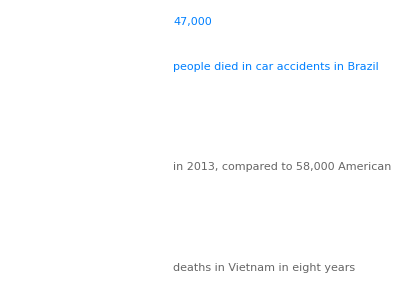

```mathematica
genLines[lines_, startPt_, spacing_, offset_, opts:OptionsPattern[Style]] := 	
	Table[Style[Text[lines⟦n+1⟧, startPt - n{0,spacing}, offset],
		  opts], {n, 0, Length[lines]-1}]

tintedColour[colour_, intensity_] := 
	Apply[RGBColor, (1-colour)*(1-intensity) + colour]

hlColour = tintedColour[{0,0.5,1}, 1];
spacing = 25;
Graphics[{
	Style[Text["47,000", {0, 10}, {-1,-1}],
		  Bold, hlColour, FontSize->100],
	Style[Text["people died in car accidents in Brazil",
		       {0, -1}, {-1,-1}],
		  hlColour, FontSize->20],
	
	Style[Text[Row[{Style["in 2013", hlColour],	
		           ", compared to 58,000 American"}],
		       {0, -1-spacing}, {-1,-1}],
		  GrayLevel[0.4], FontSize->20],  
	Style[Text["deaths in Vietnam in eight years",
		       {0, -1-2spacing}, {-1,-1}],
		  GrayLevel[0.4], FontSize->20]
}]
```

### Misleading plots and ethics in data visualisation

The American tv network Fox News showed a version of this plot in 2012:

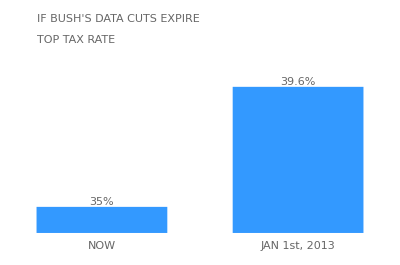

```mathematica
data = {35, 39.6};
dataLabels = Map[Row[{#, "%"}]&, data];
labels = {"NOW", "JAN 1st, 2013"};
width = 5;

Graphics[{
	{EdgeForm[None], hlBlue,
	Rectangle[{0,34},{width,data⟦1⟧}]},
	{EdgeForm[None], hlBlue,
	Rectangle[{1.5 width, 34},{2.5 width,data⟦2⟧}]},
	Style[Text[labels⟦1⟧, {width/2, 33.7}, {0,1}],
		  GrayLevel[0.4], FontSize->18],
	Style[Text[labels⟦2⟧, {2width, 33.7}, {0,1}],
		  GrayLevel[0.4], FontSize->18],
	Style[Text[dataLabels⟦1⟧, {width/2, data⟦1⟧}, {0,-1}],
		  GrayLevel[0.4], FontSize->18],
	Style[Text[dataLabels⟦2⟧, {2width, data⟦2⟧}, {0,-1}],
		  GrayLevel[0.4], FontSize->18],
	Style[Text["IF BUSH'S DATA CUTS EXPIRE", 
		       {0, 42}, {-1,-1}],
		  GrayLevel[0.4], FontSize->20],
	Style[Text["TOP TAX RATE", 
		       {0, 41.2}, {-1,-1}],
		  GrayLevel[0.4], FontSize->16]
}]
```

This plot seems to show a huge difference in tax rates after the cuts expire, but look at the numbers: the difference is not very large! The bars in this chart are drawn with an origin not at zero, but at 34%. This is extremely misleading. We instinctively associate the lengths of the bars in a bar chart to the magnitude of the quantity being displayed; plotting a bar chart with a non-zero origin is almost always a bad idea. Here is the two quantities plotted properly:

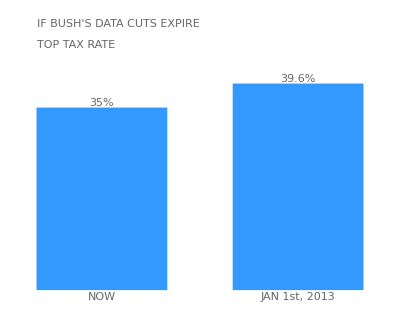

```mathematica
data = {35, 39.6};
dataLabels = Map[Row[{#, "%"}]&, data];
labels = {"NOW", "JAN 1st, 2013"};
width = 25;

Graphics[{
	{EdgeForm[None], hlBlue,
	Rectangle[{0,0},{width,data⟦1⟧}]},
	{EdgeForm[None], hlBlue,
	Rectangle[{1.5 width, 0},{2.5 width,data⟦2⟧}]},
	Style[Text[labels⟦1⟧, {width/2, -0.3}, {0,1}],
		  GrayLevel[0.4], FontSize->18],
	Style[Text[labels⟦2⟧, {2width, -0.3}, {0,1}],
		  GrayLevel[0.4], FontSize->18],
	Style[Text[dataLabels⟦1⟧, {width/2, data⟦1⟧}, {0,-1}],
		  GrayLevel[0.4], FontSize->18],
	Style[Text[dataLabels⟦2⟧, {2width, data⟦2⟧}, {0,-1}],
		  GrayLevel[0.4], FontSize->18],
	Style[Text["IF BUSH'S DATA CUTS EXPIRE", 
		       {0, 50}, {-1,-1}],
		  GrayLevel[0.4], FontSize->20],
	Style[Text["TOP TAX RATE", 
		       {0, 46}, {-1,-1}],
		  GrayLevel[0.4], FontSize->16]
}]
```

This example highlights the ethical issues around data analysis. Even if you do not tamper with the data or hide relevant data, the way you present data can be purposefully misleading. This is a violation of the implicit trust that must exist between you and your audience, and you should never do this.

## The principles of visual perception

Psychology has for many years studied the ways our brains group up and associate objects we see, and has come up with a list of a few general principles that govern how we visually perceive the world. It is important to understand those principles, because they will allow us to organise our visuals better. They will also help us spot features in our graphs that serve no useful purpose, and act as visual distractions.

### Proximity

We perceive objects that are close to each other to be part of the same group. Consider these two figures:

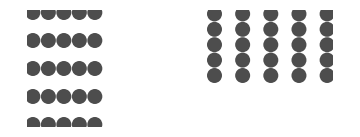

You see the dots in the left figure organised in rows, because they are closer in the horizontal than in the vertical direction. In contrast, you see the dots in the right figure organised in columns, because the dots are closer in the vertical direction. Another way of saying this is that there are clear whitespace separating the rows of dots on the left, and the columns on the right.

This principle can be seen in one of our examples:

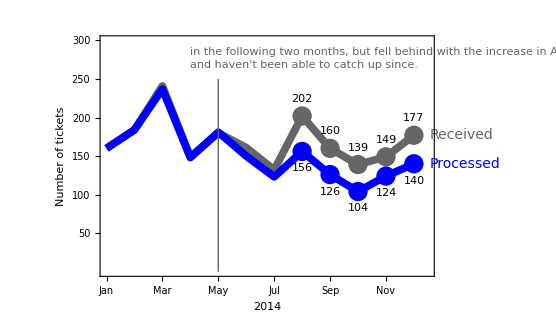

Looking at the data points for August and later months, it is obvious which point each label refers to, largely because each label is close to, and aligned with, the point it is labeling. Here is an alternative way this could have been done:

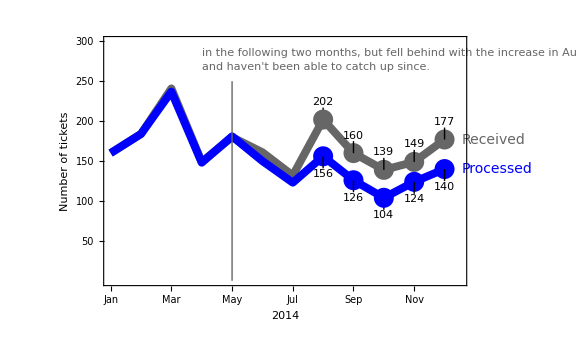

Now we have lines connecting the points and the corresponding labels. But those are completely unnecessary, because the association between labels and points is already well established by their proximity (and by their colours). Notice that proximity and colour established a connection between points and labels without introducing new elements to the plot, and therefore without complicating it. The connecting lines we added do nothing here; they are just visual pollution, clutter that we should get rid of.

### Similarity

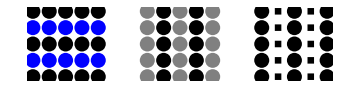

We tend to group together objects that are similar in a way that is visually striking. For data visualisation, the most important similarities are colour, shape, and tint (how solid/faded they look).

This is used in our example:

The numbers labeling the later points have the same colour as the points, and the points have the same colour as their lines. The labels “Received” and “Processed” also share a colour with the data they are describing. Colour and tint create very powerful associations in our heads, and their use should always be constrained and deliberate. So please don’t do this:

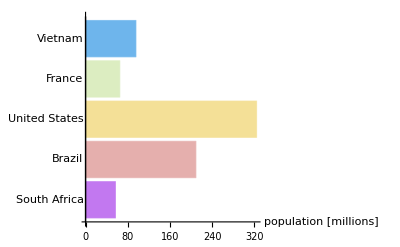

The colours here are completely redundant, since each bar is already labeled by the name of the corresponding country.

### Enclosure

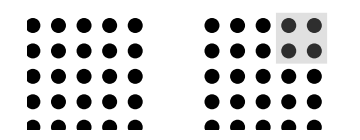

Placing a group of objects within a region defined by an outline or by a color/shading different from the background will group them. This is used in this example:

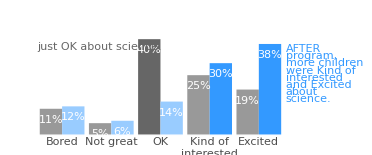

The percentages are inside the bars, so we have no trouble identifying which number corresponds to which bar.

However, enclosure is very often misused:

Surrounding this plot with a frame only adds visual noise. All the elements of the plot are clearly part of the same chart, so this does not need to be shown by the frame.

### Continuity

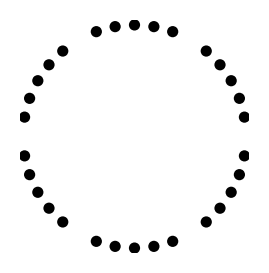

Even though some points are missing, you still see a circle when you look at the figure above; your mind fills the gaps. This is used all the time in data visualisation. For example, we still see dashed lines as lines, despite the fact that they are just disjointed segments of lines. As another example, consider any bar chart:

We do not need a horizontal axis, because we automatically assume that the bars are aligned on the bottom, so we can think of their heights as measures of the quantity being displayed. Adding a horizontal axis to bar charts is almost always a bad idea, because they don’t add anything to the plot - they are visual distractions.

### Connection

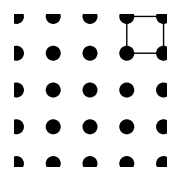

Connecting objects through lines strongly suggests they are associated. We have already seen an example of bad use of this:

But the same plot also shows a good use of connection:

The line connecting the month of May to the text explaining what happened is a good use of the principle of connection. The same line also goes through the plot lines, indicating exactly when that is on the data series.

## Remove visual distractions!

Every single element present in a graph requires some brain power to process it. This is known as cognitive load. Every additional line, symbol, text, or colour makes your plot a little more difficult to understand. This means that everything on your graph should be there for a good reason. You should be able to say what every feature on your plot is doing for you. If the answer is “nothing”, that feature needs to go. Conciseness is a precious quality in any form of communication; data visualisation is no different. 

The principles of visual perception will help you detect visual distractions, and will guide you towards better ways to associate different elements of your graphs. Let us consider a version of a familiar plot with many visual distractions, and compare it with the actual version to see how much better it becomes after we clean it up.

Before:

After:

## Challenges

1. The following plot has the goal of demonstrating that India’s population will overtake China’s in a few years, and become the most populous country on Earth. Fix it by getting rid of the visual distractions.

```mathematica
popChina = Table[{year, CountryData["China", {{"Population"}, year}]/1000000},
				  {year, 1950, 2017, 2}];
popIndia = Table[{year, CountryData["India", {{"Population"}, year}]/1000000},
				  {year, 1950, 2017, 2}];
popBrazil = Table[{year, CountryData["Brazil", {{"Population"}, year}]/1000000},
				  {year, 1950, 2017, 2}];
forecastChina = {Last@popChina//QuantityMagnitude, {2030, 1500}};
forecastIndia = {Last@popIndia//QuantityMagnitude, {2030, 1550}};

ListPlot[{popChina, popIndia, popBrazil, forecastChina, forecastIndia},
	Joined->True, Mesh->All,
	Frame->True,
	GridLines->Automatic,
	FrameLabel->{"year", "population [millions]"},
	PlotLabel->"India will soon have the largest population in the world",
	PlotLegends->{"China", "India", "Brazil", "forecast for China", "forecast for India"},
	
	Epilog->{
		Text[Framed@"pop growth slows down", {1984,1300}, {1,-1}],
		Arrow[{{1975,1290}, {1990,1200}}],
		Text[Framed@"pop does not slow down", {1990,500}, {-1,-1}],
		Arrow[{{2002,700}, {1990,850}}],
		Red,
		Text[Framed@"year 2025", {2020,1200}, {0,1}],
		Arrow[{{2020,1210}, {2023,1400}}]
	}
]
```

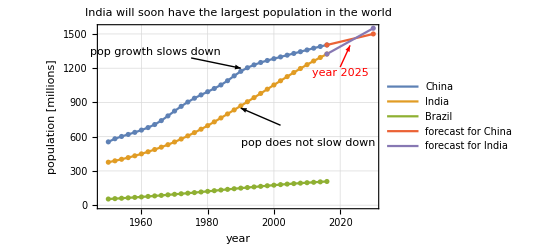

2. Make a plot that shows convincingly that there is a strong correlation between high literacy rates and low infant mortality. Choose some continent or region to highlight in your plot. Focus on creating a clean, clear plot, and avoiding visual distractions.